## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="G3PD2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_G3PD2";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

ordered bi bi; [nadp,glyc3p,dhap,nadph]

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | glyc3p,Null;nadp,Null | 0.000024 | 0.0000228
0.0000252 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadph | 3.4×10^-6 | 3.23×10^-6
3.57×10^-6 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | dhap | 0.00018 | 0.000171
0.000189 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | nadp | 0.000165 | 0.00015675
0.00017325 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | glyc3p | 0.00003 | 0.0000285
0.0000315 |  | M | 7.4 | 23 | trishcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | glyc3p | 4.2×10^-6 | 3.99×10^-6
4.41×10^-6 | nadph | 0.0001 | Competitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | glyc3p | 6.5×10^-6 | 6.175×10^-6
6.825×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | glyc3p | 2.5×10^-6 | 2.375×10^-6
2.625×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadp | 0.000187 | 0.00017765
0.00019635 | dhap | 0.002 | Competitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | dhap | 0.000038 | 0.0000361
0.0000399 | nadp | 0.002 | Competitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | dhap | 0.00024 | 0.000228
0.000252 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | dhap | 0.00012 | 0.000114
0.000126 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadph | 8.×10^-7 | 7.6×10^-7
8.4×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadph | 6.×10^-7 | 5.7×10^-7
6.3×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadph | 4.×10^-7 | 3.8×10^-7
4.2×10^-7 | glyc3p | 0.0002 | Competitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1,1};
s05Priorities = Null;
kcatPriorities = Null;
inhibitionPriorities={1,1,1, 1,1,1,1,1,1,1,1,1};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

ordered bi bi; [nadp,glyc3p,dhap,nadph]

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | glyc3p,Null;nadp,Null | 0.000024 | 0.0000228
0.0000252 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nadph | 3.4×10^-6 | 3.23×10^-6
3.57×10^-6 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | dhap | 0.00018 | 0.000171
0.000189 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | nadp | 0.000165 | 0.00015675
0.00017325 |  | M | 7.4 | 23 | trishcl | 0.1 | 
1 | glyc3p | 0.00003 | 0.0000285
0.0000315 |  | M | 7.4 | 23 | trishcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | glyc3p | 4.2×10^-6 | 3.99×10^-6
4.41×10^-6 | nadph | 0.0001 | Competitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | glyc3p | 6.5×10^-6 | 6.175×10^-6
6.825×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | glyc3p | 2.5×10^-6 | 2.375×10^-6
2.625×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadp | 0.000187 | 0.00017765
0.00019635 | dhap | 0.002 | Competitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | dhap | 0.000038 | 0.0000361
0.0000399 | nadp | 0.002 | Competitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | dhap | 0.00024 | 0.000228
0.000252 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | dhap | 0.00012 | 0.000114
0.000126 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincu | nadph | 8.×10^-7 | 7.6×10^-7
8.4×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kincc | nadph | 6.×10^-7 | 5.7×10^-7
6.3×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
1 | Kic | nadph | 4.×10^-7 | 3.8×10^-7
4.2×10^-7 | glyc3p | 0.0002 | Competitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

```mathematica
{{"ordered bi bi"}, {"\"[nadp,glyc3p,dhap,nadph]\""}}
```

```mathematica
catalyticBranch={"E_G3PD2[c] + nadp[c] <=> E_G3PD2[c]&nadp",
				"E_G3PD2[c]&nadp + glyc3p[c] <=> E_G3PD2[c]&nadp&glyc3p",
				"E_G3PD2[c]&nadp&glyc3p <=> E_G3PD2[c]&nadph&dhap",
				"E_G3PD2[c]&nadph&dhap <=> E_G3PD2[c]&nadph + dhap[c]",
				"E_G3PD2[c]&nadph <=> E_G3PD2[c] + nadph[c]"};


enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites-> 0];
enzymeModelOrig["Reactions"]
nActiveSites=1;
```

{((G3PD2^c)_^+nadp^c⇌(G3PD2^c&nadp^c)_^)^G3PD21,((G3PD2^c&nadph^c)_^⇌(G3PD2^c)_^+nadph^c)^G3PD22,((G3PD2^c&nadp^c)_^+glyc3p^c⇌(G3PD2^c&nadp^c&glyc3p^c)_^)^G3PD23,((G3PD2^c&nadph^c&dhap^c)_^⇌(G3PD2^c&nadph^c)_^+dhap^c)^G3PD24,((G3PD2^c&nadp^c&glyc3p^c)_^⇌(G3PD2^c&nadph^c&dhap^c)_^)^G3PD25}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((G3PD2^c)_^+nadp^c⇌(G3PD2^c&nadp^c)_^)^G3PD21,Overscript[(G3PD2^c&nadph^c)_^⇌(G3PD2^c)_^+nadph^c, G3PD22],((G3PD2^c&nadp^c)_^+glyc3p^c⇌(G3PD2^c&nadp^c&glyc3p^c)_^)^G3PD23,Overscript[(G3PD2^c&nadph^c&dhap^c)_^⇌(G3PD2^c&nadph^c)_^+dhap^c, G3PD24],((G3PD2^c&nadp^c&glyc3p^c)_^⇌(G3PD2^c&nadph^c&dhap^c)_^)^G3PD25};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

### Setup King-Altman Equations

#### Define some parameters

```mathematica
Get["MASSef`"]
```

```mathematica
inputPath="test_files/build_module"
```

test_files/build_module

```mathematica
Export["G3PD2setUpFluxEquationsArguments.mx", {enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,inhibitionList[[{2,3,8,9}]], catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub, MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites}]
```

G3PD2setUpFluxEquationsArguments.mx

```mathematica
Export["G3PD2setUpFluxEquationsTrueRes.mx",{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse},"MX"];
```

```mathematica
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, otherAbsoluteRatesForward, otherAbsoluteRatesReverse}
```

/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag =True;
simplifyMaxTime=30;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={{"prod_inhib_dhap", nadph^c->0},{ "prod_inhib_nadph", dhap^c->0}};
otherMetsForwardZeroSub={{"prod_inhib_glyc3p", nadp^c->0},{"prod_inhib_nadp", glyc3p^c->0}};
```

```mathematica
{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,inhibitionList[[{2,3,8,9}]], catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub, MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{glyc3p^c→0,nadp^c→0}

{dhap^c→0,nadph^c→0}

{glyc3p^c→∞,nadp^c→∞}

{dhap^c→∞,nadph^c→∞}

prod inhib

{((G3PD2^c&nadp^c&glyc3p^c)_^-((G3PD2^c&nadph^c&dhap^c)_^)/K_G3PD25) Volume_c k_G3PD25^⟶}

Volume_c (-(G3PD2^c&nadph^c&dhap^c)_^ k_G3PD25^⟵+(G3PD2^c&nadp^c&glyc3p^c)_^ k_G3PD25^⟶)

1

2

3

0.27255

4

0.000667

5

0.00009

Simplifying...

6

0.13104

{((G3PD2^c&nadph^c)_^+glyc3p^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_Kincu_glyc3p_1_nadph,((G3PD2^c)_^+glyc3p^c⇌(G3PD2^c&glyc3p^c)_^)^G3PD2_Kincc_glyc3p_1_nadph,((G3PD2^c&glyc3p^c)_^+nadph^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_NC_glyc3p,((G3PD2^c&nadp^c)_^+dhap^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_Kincu_dhap_1_nadp,((G3PD2^c)_^+dhap^c⇌(G3PD2^c&dhap^c)_^)^G3PD2_Kincc_dhap_1_nadp,((G3PD2^c&dhap^c)_^+nadp^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_NC_dhap}

{}

{((G3PD2^c&nadp^c&glyc3p^c)_^-((G3PD2^c&nadph^c&dhap^c)_^)/K_G3PD25) Volume_c k_G3PD25^⟶}

{((G3PD2^c&nadp^c&glyc3p^c)_^-((G3PD2^c&nadph^c&dhap^c)_^)/K_G3PD25) Volume_c k_G3PD25^⟶}

Volume_c (-(G3PD2^c&nadph^c&dhap^c)_^ k_G3PD25^⟵+(G3PD2^c&nadp^c&glyc3p^c)_^ k_G3PD25^⟶)

1

2

3

33.73799

4

0.01477

5

0.000623

Simplifying...

6

59.995089

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating other relative rate forward equation.
..

Simplifying...

{prod_inhib_dhap,nadph^c→0}

{glyc3p^c→∞,nadp^c→∞}

{prod_inhib_nadph,dhap^c→0}

{glyc3p^c→∞,nadp^c→∞}

Generating other relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
Simplify@otherAbsoluteRatesForward[[1]]
```

{otherRateRelFor_glyc3p_prod_inhib_dhap,(glyc3p^c k_G3PD23^⟶ (k_G3PD22^⟶ k_G3PD24^⟶ k_G3PD25^⟶+nadp^c k_G3PD21^⟶ (k_G3PD24^⟶ k_G3PD25^⟶+dhap^c k_G3PD24^⟵ (k_G3PD25^⟵+k_G3PD25^⟶)+k_G3PD22^⟶ (k_G3PD24^⟶+k_G3PD25^⟵+k_G3PD25^⟶))) k_G3PD2_Kincc_glyc3p_1_nadph^⟵ (dhap^c k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶+k_G3PD21^⟶ (k_G3PD2_Kincc_dhap_1_nadp^⟵ (k_G3PD2_Kincu_dhap_1_nadp^⟵+k_G3PD2_NC_dhap^⟵)+nadp^c k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶)) (glyc3p^c k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_glyc3p^⟵+k_G3PD22^⟶ (k_G3PD2_Kincu_glyc3p_1_nadph^⟵+k_G3PD2_NC_glyc3p^⟵)))/(k_G3PD21^⟶ k_G3PD22^⟶ (dhap^c glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟵ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟵+dhap^c glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟵+glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟵+(glyc3p^c)^2 nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶+dhap^c glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟵ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟵ k_G3PD2_NC_dhap^⟵+dhap^c glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟵ k_G3PD2_NC_dhap^⟵+glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟵ k_G3PD2_NC_dhap^⟵+(glyc3p^c)^2 nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵+dhap^c glyc3p^c (nadp^c)^2 k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟵ k_G3PD2_NC_dhap^⟶+dhap^c glyc3p^c (nadp^c)^2 k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟵ k_G3PD2_NC_dhap^⟶+glyc3p^c (nadp^c)^2 k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟵ k_G3PD2_NC_dhap^⟶+(dhap^c)^2 glyc3p^c nadp^c k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟵ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟵ k_G3PD2_NC_dhap^⟶+(dhap^c)^2 glyc3p^c nadp^c k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟵ k_G3PD2_NC_dhap^⟶+dhap^c glyc3p^c nadp^c k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟵ k_G3PD2_NC_dhap^⟶+(glyc3p^c)^2 (nadp^c)^2 k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶+dhap^c (glyc3p^c)^2 nadp^c k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶+dhap^c glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟵ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_glyc3p^⟵+dhap^c glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_glyc3p^⟵+glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD25^⟵ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_glyc3p^⟵+glyc3p^c k_G3PD21^⟵ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_glyc3p^⟵+glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_glyc3p^⟵+dhap^c glyc3p^c k_G3PD21^⟵ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_glyc3p^⟵+dhap^c (glyc3p^c)^2 k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 k_G3PD21^⟵ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟶ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^3 k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟶ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_glyc3p^⟵+dhap^c glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟶ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_glyc3p^⟵+dhap^c glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟵ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+dhap^c glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD25^⟵ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 nadp^c k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+glyc3p^c k_G3PD21^⟵ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+dhap^c glyc3p^c k_G3PD21^⟵ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+dhap^c (glyc3p^c)^2 k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 k_G3PD21^⟵ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟶ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^3 k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟶ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+dhap^c glyc3p^c nadp^c k_G3PD21^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟶ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+dhap^c glyc3p^c k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟶ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+(dhap^c)^2 glyc3p^c k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟶ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+dhap^c (glyc3p^c)^2 k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟶ k_G3PD2_Kincu_dhap_1_nadp^⟶ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟵ k_G3PD2_NC_glyc3p^⟵+dhap^c glyc3p^c (nadp^c)^2 k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+dhap^c glyc3p^c (nadp^c)^2 k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+glyc3p^c (nadp^c)^2 k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+(dhap^c)^2 glyc3p^c nadp^c k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟵ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+(dhap^c)^2 glyc3p^c nadp^c k_G3PD23^⟶ k_G3PD24^⟵ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+dhap^c glyc3p^c nadp^c k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+dhap^c glyc3p^c nadp^c k_G3PD21^⟵ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+dhap^c (glyc3p^c)^2 nadp^c k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 (nadp^c)^2 k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+dhap^c (glyc3p^c)^2 nadp^c k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 (nadp^c)^2 k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 (nadp^c)^2 k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD25^⟵ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 (nadp^c)^2 k_G3PD21^⟶ k_G3PD23^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+glyc3p^c nadp^c k_G3PD21^⟵ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+glyc3p^c (nadp^c)^2 k_G3PD21^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 nadp^c k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+dhap^c (glyc3p^c)^2 nadp^c k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+dhap^c (glyc3p^c)^2 nadp^c k_G3PD23^⟶ k_G3PD25^⟵ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+dhap^c (glyc3p^c)^2 nadp^c k_G3PD23^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+dhap^c glyc3p^c nadp^c k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^2 nadp^c k_G3PD21^⟵ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟶ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+(glyc3p^c)^3 nadp^c k_G3PD23^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟶ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+dhap^c glyc3p^c (nadp^c)^2 k_G3PD21^⟶ k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟶ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+(dhap^c)^2 glyc3p^c nadp^c k_G3PD24^⟶ k_G3PD25^⟶ k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟶ k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_dhap^⟶ k_G3PD2_NC_glyc3p^⟵+k_G3PD22^⟶ (glyc3p^c nadp^c k_G3PD23^⟶ (k_G3PD25^⟵+k_G3PD25^⟶) k_G3PD2_Kincc_glyc3p_1_nadph^⟵ (dhap^c k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶+k_G3PD21^⟶ (k_G3PD2_Kincc_dhap_1_nadp^⟵ (k_G3PD2_Kincu_dhap_1_nadp^⟵+k_G3PD2_NC_dhap^⟵)+nadp^c k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶))+k_G3PD23^⟵ (k_G3PD24^⟶+k_G3PD25^⟵) (k_G3PD2_Kincc_dhap_1_nadp^⟵ (dhap^c (k_G3PD2_Kincc_glyc3p_1_nadph^⟵+glyc3p^c k_G3PD2_Kincc_glyc3p_1_nadph^⟶) k_G3PD2_Kincu_dhap_1_nadp^⟶ k_G3PD2_NC_dhap^⟵+k_G3PD21^⟵ (k_G3PD2_Kincc_glyc3p_1_nadph^⟵+glyc3p^c k_G3PD2_Kincc_glyc3p_1_nadph^⟶) (k_G3PD2_Kincu_dhap_1_nadp^⟵+k_G3PD2_NC_dhap^⟵)+nadp^c k_G3PD21^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ (k_G3PD2_Kincu_dhap_1_nadp^⟵+dhap^c k_G3PD2_Kincu_dhap_1_nadp^⟶+k_G3PD2_NC_dhap^⟵))+nadp^c ((nadp^c k_G3PD21^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵+k_G3PD21^⟵ (k_G3PD2_Kincc_glyc3p_1_nadph^⟵+glyc3p^c k_G3PD2_Kincc_glyc3p_1_nadph^⟶)) k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶+dhap^c k_G3PD21^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟶ (k_G3PD2_NC_dhap^⟵+nadp^c k_G3PD2_NC_dhap^⟶))+dhap^c k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ (nadp^c k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶+dhap^c k_G3PD2_Kincu_dhap_1_nadp^⟶ (k_G3PD2_NC_dhap^⟵+nadp^c k_G3PD2_NC_dhap^⟶)+k_G3PD21^⟵ (k_G3PD2_Kincu_dhap_1_nadp^⟵+k_G3PD2_NC_dhap^⟵+nadp^c k_G3PD2_NC_dhap^⟶)))+k_G3PD24^⟶ (glyc3p^c nadp^c k_G3PD23^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ (dhap^c k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶+k_G3PD21^⟶ (k_G3PD2_Kincc_dhap_1_nadp^⟵ (k_G3PD2_Kincu_dhap_1_nadp^⟵+k_G3PD2_NC_dhap^⟵)+nadp^c k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶))+k_G3PD25^⟶ (k_G3PD2_Kincc_dhap_1_nadp^⟵ (k_G3PD21^⟵ (k_G3PD2_Kincc_glyc3p_1_nadph^⟵+glyc3p^c k_G3PD2_Kincc_glyc3p_1_nadph^⟶) (k_G3PD2_Kincu_dhap_1_nadp^⟵+k_G3PD2_NC_dhap^⟵)+nadp^c k_G3PD21^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ (k_G3PD2_Kincu_dhap_1_nadp^⟵+dhap^c k_G3PD2_Kincu_dhap_1_nadp^⟶+k_G3PD2_NC_dhap^⟵)+(k_G3PD2_Kincc_glyc3p_1_nadph^⟵+glyc3p^c k_G3PD2_Kincc_glyc3p_1_nadph^⟶) (dhap^c k_G3PD2_Kincu_dhap_1_nadp^⟶ k_G3PD2_NC_dhap^⟵+glyc3p^c k_G3PD23^⟶ (k_G3PD2_Kincu_dhap_1_nadp^⟵+k_G3PD2_NC_dhap^⟵)))+nadp^c ((nadp^c k_G3PD21^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵+k_G3PD21^⟵ (k_G3PD2_Kincc_glyc3p_1_nadph^⟵+glyc3p^c k_G3PD2_Kincc_glyc3p_1_nadph^⟶)+glyc3p^c k_G3PD23^⟶ (k_G3PD2_Kincc_glyc3p_1_nadph^⟵+glyc3p^c k_G3PD2_Kincc_glyc3p_1_nadph^⟶)) k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶+dhap^c k_G3PD21^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ k_G3PD2_Kincu_dhap_1_nadp^⟶ (k_G3PD2_NC_dhap^⟵+nadp^c k_G3PD2_NC_dhap^⟶))+dhap^c k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ (dhap^c k_G3PD2_Kincu_dhap_1_nadp^⟶ k_G3PD2_NC_dhap^⟵+nadp^c k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶+dhap^c nadp^c k_G3PD2_Kincu_dhap_1_nadp^⟶ k_G3PD2_NC_dhap^⟶+k_G3PD21^⟵ (k_G3PD2_Kincu_dhap_1_nadp^⟵+k_G3PD2_NC_dhap^⟵+nadp^c k_G3PD2_NC_dhap^⟶)+glyc3p^c k_G3PD23^⟶ (k_G3PD2_Kincu_dhap_1_nadp^⟵+k_G3PD2_NC_dhap^⟵+nadp^c k_G3PD2_NC_dhap^⟶))))) (k_G3PD2_Kincu_glyc3p_1_nadph^⟵+k_G3PD2_NC_glyc3p^⟵)+k_G3PD23^⟵ (dhap^c (dhap^c k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵+k_G3PD2_Kincc_dhap_1_nadp^⟵ (k_G3PD2_Kincc_glyc3p_1_nadph^⟵+glyc3p^c k_G3PD2_Kincc_glyc3p_1_nadph^⟶)) k_G3PD2_Kincu_dhap_1_nadp^⟶ k_G3PD2_NC_dhap^⟵+(nadp^c)^2 k_G3PD21^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ (k_G3PD2_Kincu_dhap_1_nadp^⟵+dhap^c k_G3PD2_Kincu_dhap_1_nadp^⟶) k_G3PD2_NC_dhap^⟶+nadp^c k_G3PD2_Kincc_glyc3p_1_nadph^⟵ (k_G3PD21^⟶ (dhap^c k_G3PD2_Kincu_dhap_1_nadp^⟶ k_G3PD2_NC_dhap^⟵+k_G3PD2_Kincc_dhap_1_nadp^⟵ (k_G3PD2_Kincu_dhap_1_nadp^⟵+dhap^c k_G3PD2_Kincu_dhap_1_nadp^⟶+k_G3PD2_NC_dhap^⟵))+dhap^c k_G3PD2_Kincc_dhap_1_nadp^⟶ (k_G3PD2_Kincu_dhap_1_nadp^⟵+dhap^c k_G3PD2_Kincu_dhap_1_nadp^⟶) k_G3PD2_NC_dhap^⟶)+k_G3PD21^⟵ (k_G3PD2_Kincc_dhap_1_nadp^⟵ (k_G3PD2_Kincc_glyc3p_1_nadph^⟵+glyc3p^c k_G3PD2_Kincc_glyc3p_1_nadph^⟶) (k_G3PD2_Kincu_dhap_1_nadp^⟵+k_G3PD2_NC_dhap^⟵)+nadp^c (k_G3PD2_Kincc_glyc3p_1_nadph^⟵+glyc3p^c k_G3PD2_Kincc_glyc3p_1_nadph^⟶) k_G3PD2_Kincu_dhap_1_nadp^⟵ k_G3PD2_NC_dhap^⟶+dhap^c k_G3PD2_Kincc_dhap_1_nadp^⟶ k_G3PD2_Kincc_glyc3p_1_nadph^⟵ (k_G3PD2_Kincu_dhap_1_nadp^⟵+k_G3PD2_NC_dhap^⟵+nadp^c k_G3PD2_NC_dhap^⟶))) (glyc3p^c (k_G3PD24^⟶+k_G3PD25^⟵) k_G3PD2_Kincu_glyc3p_1_nadph^⟶ k_G3PD2_NC_glyc3p^⟵+dhap^c k_G3PD24^⟵ k_G3PD25^⟵ (k_G3PD2_Kincu_glyc3p_1_nadph^⟵+k_G3PD2_NC_glyc3p^⟵))))}

```mathematica
enzymeModel["Reactions"]
```

{((G3PD2^c)_^+nadp^c⇌(G3PD2^c&nadp^c)_^)^G3PD21,((G3PD2^c&nadph^c)_^⇌(G3PD2^c)_^+nadph^c)^G3PD22,((G3PD2^c&nadp^c)_^+glyc3p^c⇌(G3PD2^c&nadp^c&glyc3p^c)_^)^G3PD23,((G3PD2^c&nadph^c&dhap^c)_^⇌(G3PD2^c&nadph^c)_^+dhap^c)^G3PD24,((G3PD2^c&nadp^c&glyc3p^c)_^⇌(G3PD2^c&nadph^c&dhap^c)_^)^G3PD25,((G3PD2^c&nadph^c)_^+glyc3p^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_Kincu_glyc3p_1_nadph,((G3PD2^c)_^+glyc3p^c⇌(G3PD2^c&glyc3p^c)_^)^G3PD2_Kincc_glyc3p_1_nadph,((G3PD2^c&glyc3p^c)_^+nadph^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_NC_glyc3p,((G3PD2^c&nadp^c)_^+dhap^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_Kincu_dhap_1_nadp,((G3PD2^c)_^+dhap^c⇌(G3PD2^c&dhap^c)_^)^G3PD2_Kincc_dhap_1_nadp,((G3PD2^c&dhap^c)_^+nadp^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_NC_dhap}

```mathematica
nonCatalyticReactions
```

{}

```mathematica
trueRes={{((G3PD2^c&nadph^c)_^+glyc3p^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_Kincu_glyc3p_1_nadph}, {((G3PD2^c)_^+glyc3p^c⇌(G3PD2^c&glyc3p^c)_^)^G3PD2_Kincc_glyc3p_1_nadph}, {((G3PD2^c&glyc3p^c)_^+nadph^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_NC_glyc3p}, {((G3PD2^c&nadp^c)_^+dhap^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_Kincu_dhap_1_nadp}, {((G3PD2^c)_^+dhap^c⇌(G3PD2^c&dhap^c)_^)^G3PD2_Kincc_dhap_1_nadp}, {((G3PD2^c&dhap^c)_^+nadp^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_NC_dhap}};
SameQ[trueRes, nonCatalyticReactions]
```

True

```mathematica
unifiedRateConstList
```

{}

## Semi-Automated Simulate Data

```mathematica
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
Export["G3PD2SimulateDataArguments.mx",{enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList}, "MX"];
Export["G3PD2SimulateDataResults.mx",{allFittingData, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	glyc3p[c]	nadp[c]	nadph[c]	param_G3PD2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
1	0.01	0	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.09090909090909097
1	0.01	0	0	5.388636854367791e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.1368068886032101
1	0.01	0	0	8.540413867132584e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.20076000891310194
1	0.01	0	0	1.3535643798818904e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.2847472489508014
1	0.01	0	0	2.1452549712326573e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.386863179846857
1	0.01	0	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.5000000000000001
1	0.01	0	0	5.388636854367791e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.6131368201531433
1	0.01	0	0	8.540413867132584e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.7152527510491989
1	0.01	0	0	0.000013535643798818902	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.7992399910868982
1	0.01	0	0	0.000021452549712326573	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.86319311139679
1	0.01	0	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.9090909090909091
1	0.000018000000000000017	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.09090909090909098
1	0.00002852807746430008	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.13680688860321016
1	0.00004521395576717252	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.200760008913102
1	0.00007165929069962952	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.28474724895080145
1	0.00011357232200643484	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.38686317984685703
1	0.00018000000000000017	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.5000000000000002
1	0.0002852807746430008	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.6131368201531433
1	0.0004521395576717252	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.7152527510491989
1	0.0007165929069962958	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.7992399910868984
1	0.0011357232200643484	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.86319311139679
1	0.0018000000000000017	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.9090909090909092
1	0	0.01	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.09090909090909097
1	0	0.01	0.000026150737675608408	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.13680688860321016
1	0	0.01	0.000041446126119908146	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.20076000891310203
1	0	0.01	0.00006568768314132706	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.2847472489508014
1	0	0.01	0.00010410796183923194	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.3868631798468571
1	0	0.01	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.5000000000000002
1	0	0.01	0.0002615073767560841	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.6131368201531434
1	0	0.01	0.0004144612611990815	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.7152527510491989
1	0	0.01	0.0006568768314132713	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.7992399910868985
1	0	0.01	0.0010410796183923194	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.8631931113967901
1	0	0.01	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.9090909090909092
1	0	3.0000000000000013e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.09090909090909094
1	0	4.7546795773833446e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.1368068886032101
1	0	7.535659294528749e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.20076000891310194
1	0	0.000011943215116604912	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.28474724895080133
1	0	0.000018928720334405797	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.3868631798468569
1	0	0.00003000000000000001	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.5000000000000001
1	0	0.00004754679577383344	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.6131368201531432
1	0	0.00007535659294528749	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.7152527510491988
1	0	0.00011943215116604925	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.7992399910868984
1	0	0.00018928720334405796	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.86319311139679
1	0	0.00030000000000000014	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.9090909090909091
1	0.000018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.06250000000000006
1	0.000056920997883030876	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.17411239489546845
1	0.00018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.4000000000000002
1	0.0005692099788303088	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6782688399674107
1	0.0018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8695652173913044
1	0.000018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.047619047619047665
1	0.000056920997883030876	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.13652705949581442
1	0.00018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.33333333333333354
1	0.0005692099788303088	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6125741132772071
1	0.0018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8333333333333335
1	0.000018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.032258064516129066
1	0.000056920997883030876	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.09535767393826004
1	0.00018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.2500000000000002
1	0.0005692099788303088	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.5131670194948622
1	0.0018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.7692307692307694
1	0.0001	2.25e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.04914933837429115
1	0.0001	2.25e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.1359715179829786
1	0.0001	2.25e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.3080568720379148
1	0.0001	2.25e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5136142175737065
1	0.0001	2.25e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.6509764646970455
1	0.0001	4.5e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.03367875647668395
1	0.0001	4.5e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.09481652165128764
1	0.0001	4.5e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.22260273972602748
1	0.0001	4.5e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.3879359014999326
1	0.0001	4.5e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5070202808112324
1	0.0001	9.e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.0206677265500795
1	0.0001	9.e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.059062933642962216
1	0.0001	9.e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.14317180616740097
1	0.0001	9.e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.2604666499256048
1	0.0001	9.e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.351541373715522
1	0.000018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.06060606060606066
1	0.000056920997883030876	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.16016871556802817
1	0.00018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.3333333333333335
1	0.0005692099788303088	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.5064979510986386
1	0.0018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.6060606060606061
1	0.000018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.04545454545454549
1	0.000056920997883030876	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.12012653667602116
1	0.00018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.2500000000000001
1	0.0005692099788303088	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.379873463323979
1	0.0018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.4545454545454546
1	0.000018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.03030303030303033
1	0.000056920997883030876	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.08008435778401408
1	0.00018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.16666666666666674
1	0.0005692099788303088	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.2532489755493193
1	0.0018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.30303030303030304
1	0.002	0	0.0000935	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.06250000000000003
1	0.002	0	0.0000935	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1741123948954684
1	0.002	0	0.0000935	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.40000000000000013
1	0.002	0	0.0000935	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.6782688399674105
1	0.002	0	0.0000935	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8695652173913044
1	0.002	0	0.000187	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.047619047619047644
1	0.002	0	0.000187	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1365270594958144
1	0.002	0	0.000187	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.3333333333333334
1	0.002	0	0.000187	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.612574113277207
1	0.002	0	0.000187	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8333333333333334
1	0.002	0	0.000374	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.032258064516129045
1	0.002	0	0.000374	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.09535767393826002
1	0.002	0	0.000374	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.2500000000000001
1	0.002	0	0.000374	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.5131670194948621
1	0.002	0	0.000374	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.7692307692307694
1	0.000019	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.06250000000000003
1	0.000019	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.17411239489546837
1	0.000019	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.40000000000000013
1	0.000019	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.6782688399674105
1	0.000019	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8695652173913044
1	0.000038	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.04761904761904764
1	0.000038	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.13652705949581434
1	0.000038	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.3333333333333334
1	0.000038	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.612574113277207
1	0.000038	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8333333333333335
1	0.000076	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.032258064516129045
1	0.000076	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.09535767393826
1	0.000076	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.25000000000000006
1	0.000076	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.5131670194948622
1	0.000076	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.7692307692307693
1	0.00009	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.052980132450331174
1	0.00009	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.1447390418373348
1	0.00009	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.3200000000000002
1	0.00009	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.518564992170751
1	0.00009	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.6451612903225806
1	0.00018	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.03738317757009349
1	0.00018	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.10356583218373844
1	0.00018	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.235294117647059
1	0.00018	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.39361254767503817
1	0.00018	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.5000000000000001
1	0.00036	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.023529411764705903
1	0.00036	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.06601047571169773
1	0.00036	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.1538461538461539
1	0.00036	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.26561052385648354
1	0.00036	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.3448275862068966
1	0	3.0000000000000013e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.057901085645355864
1	0	9.486832980505141e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.15517252975139625
1	0	0.00003000000000000001	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.33103448275862074
1	0	0.00009486832980505142	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.5159442342521813
1	0	0.00030000000000000014	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.6266318537859008
1	0	3.0000000000000013e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.042477876106194704
1	0	9.486832980505141e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.11459214550830052
1	0	0.00003000000000000001	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.2474226804123712
1	0	0.00009486832980505142	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.39060056309756436
1	0	0.00030000000000000014	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.47808764940239046
1	0	3.0000000000000013e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.02771362586605082
1	0	9.486832980505141e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.07523930500173176
1	0	0.00003000000000000001	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.16438356164383564
1	0	0.00009486832980505142	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.2628747818212248
1	0	0.00030000000000000014	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.32432432432432434
1	0	0.0002	0.000016500000000000015	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.06250000000000006
1	0	0.0002	0.000052177581392778313	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.17411239489546848
1	0	0.0002	0.00016500000000000016	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.4000000000000002
1	0	0.0002	0.0005217758139277831	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6782688399674106
1	0	0.0002	0.0016500000000000017	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8695652173913045
1	0	0.0002	0.000016500000000000015	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.047619047619047665
1	0	0.0002	0.000052177581392778313	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.13652705949581445
1	0	0.0002	0.00016500000000000016	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.33333333333333354
1	0	0.0002	0.0005217758139277831	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6125741132772071
1	0	0.0002	0.0016500000000000017	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8333333333333335
1	0	0.0002	0.000016500000000000015	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.03225806451612906
1	0	0.0002	0.000052177581392778313	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.09535767393826007
1	0	0.0002	0.00016500000000000016	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.25000000000000017
1	0	0.0002	0.0005217758139277831	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.5131670194948623
1	0	0.0002	0.0016500000000000017	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.7692307692307693

### Sanity check plots

```mathematica
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
assumedSaturatingConc=0.01;
eTotal=1;
logStepSize=0.5;
inhibFittingData=simulateInhibData[rxn, metsFull, metSatForSub, metSatRevSub,  inhibitionList, kmList, assumedSaturatingConc, eTotal,
			   logStepSize, activeIsoSub, bufferInfo, ionCharge, inputPath, fileList];
```

#### C inhib of dhap by glyc3p

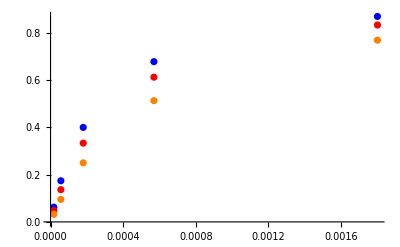

```mathematica
inhib1=inhibFittingData[[1;;5,{1,-1}]];
inhib2=inhibFittingData[[6;;10,{1,-1}]];
inhib3=inhibFittingData[[11;;15,{1,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.00027}

{1.,0.00036}

{1.,0.00054}

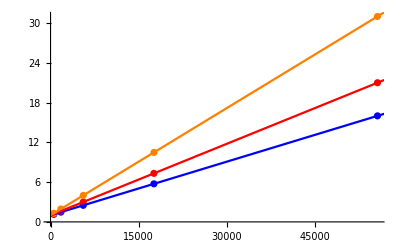

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,0,100000}, PlotStyle->{Blue,Red, Orange}]]
```

#### NC inhib of nadph by glyc3p

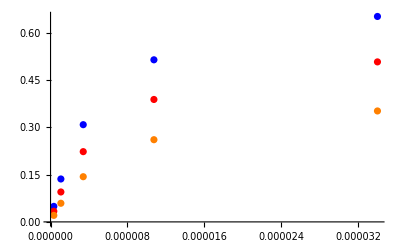

```mathematica
inhib1=inhibFittingData[[16;;20,{4,-1}]];
inhib2=inhibFittingData[[21;;25,{4,-1}]];
inhib3=inhibFittingData[[26;;30,{4,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.34615,6.46×10^-6}

{1.69231,9.52×10^-6}

{2.38462,0.00001564}

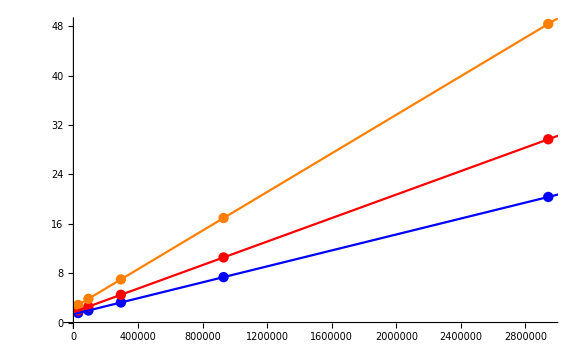

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### NC inhib of dhap by nadp

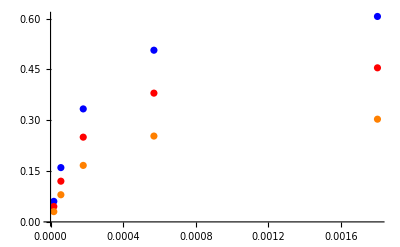

```mathematica
inhib1=inhibFittingData[[31;;35,{1,-1}]];
inhib2=inhibFittingData[[36;;40,{1,-1}]];
inhib3=inhibFittingData[[41;;45,{1,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.5,0.00027}

{2.,0.00036}

{3.,0.00054}

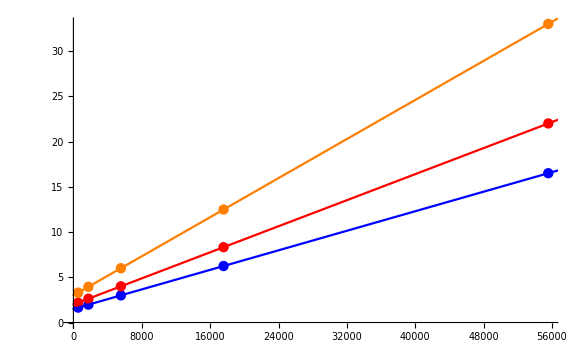

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### C inhib of nadph by nadp

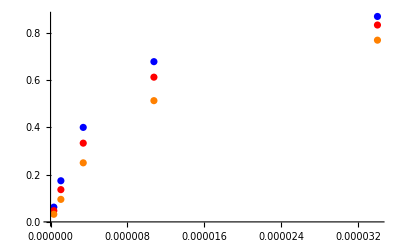

```mathematica
inhib1=inhibFittingData[[46;;50,{4,-1}]];
inhib2=inhibFittingData[[51;;55,{4,-1}]];
inhib3=inhibFittingData[[56;;60,{4,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,5.1×10^-6}

{1.,6.8×10^-6}

{1.,0.0000102}

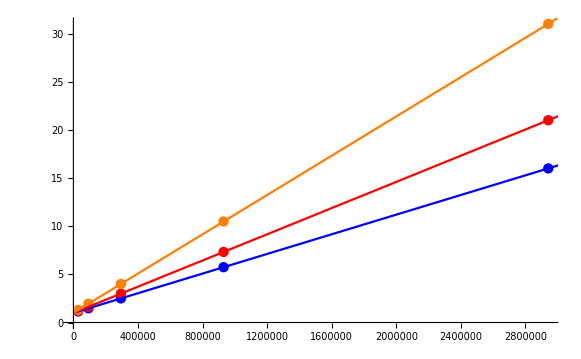

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### C inhib of glyc3p by dhap

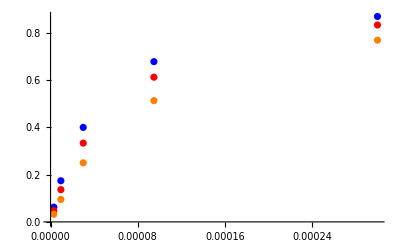

```mathematica
inhib1=inhibFittingData[[61;;65,{2,-1}]];
inhib2=inhibFittingData[[66;;70,{2,-1}]];
inhib3=inhibFittingData[[71;;75,{2,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.000045}

{1.,0.00006}

{1.,0.00009}

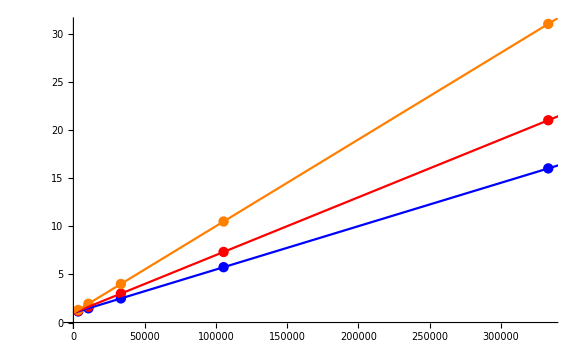

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### NC inhib of nadp by dhap

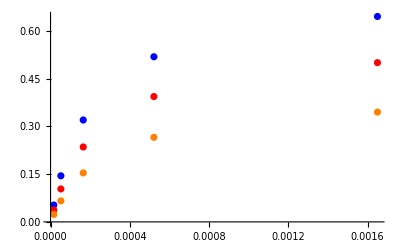

```mathematica
inhib1=inhibFittingData[[76;;80,{3,-1}]];
inhib2=inhibFittingData[[81;;85,{3,-1}]];
inhib3=inhibFittingData[[86;;90,{3,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.375,0.00028875}

{1.75,0.0004125}

{2.5,0.00066}

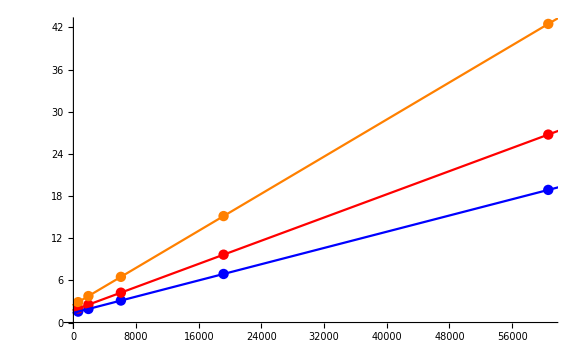

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### C inhib of nadp by nadph

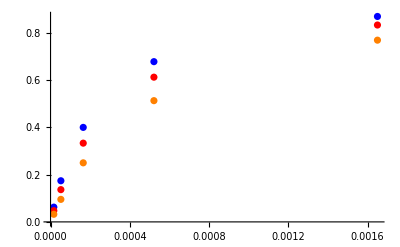

```mathematica
inhib1=inhibFittingData[[106;;110,{3,-1}]];
inhib2=inhibFittingData[[111;;115,{3,-1}]];
inhib3=inhibFittingData[[116;;120,{3,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.0002475}

{1.,0.00033}

{1.,0.000495}

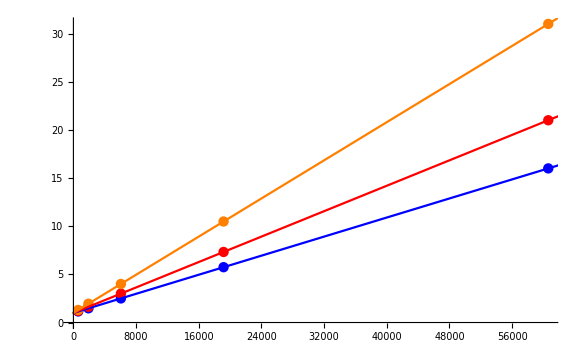

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

### Simulate data with uncertainty

```mathematica
Export["G3PD2SimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList}, "MX"];

Export["G3PD2SimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

```mathematica
FilePrint[dataPathList[[2]]]
```

Priority	dhap[c]	glyc3p[c]	nadp[c]	nadph[c]	param_G3PD2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000023303920936012922
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000023303920936012922
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000023303920936012922
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000023303920936012922
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000023303920936012922
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000023303920936012922
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000023303920936012922
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000023303920936012922
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000023303920936012922
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000023303920936012922
1	0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000023303920936012922
1	0.01	0	0	3.4946722311451653e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.09090909090909084
1	0.01	0	0	5.538682229024865e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.13680688860320994
1	0.01	0	0	8.778219759986859e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.20076000891310175
1	0.01	0	0	1.3912540739530807e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.2847472489508015
1	0.01	0	0	2.2049891107920247e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.38686317984685664
1	0.01	0	0	3.4946722311451653e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.4999999999999998
1	0.01	0	0	5.538682229024865e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.6131368201531429
1	0.01	0	0	8.778219759986858e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.7152527510491986
1	0.01	0	0	0.000013912540739530807	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.7992399910868981
1	0.01	0	0	0.000022049891107920247	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.8631931113967899
1	0.01	0	0	0.00003494672231145165	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.9090909090909091
1	0.000017627149533972375	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.09090909090909086
1	0.000027937149298886917	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.13680688860321
1	0.00004427739774057566	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.20076000891310175
1	0.00007017494625893134	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.2847472489508011
1	0.0001112197946071048	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.3868631798468567
1	0.00017627149533972373	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.4999999999999997
1	0.0002793714929888692	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.613136820153143
1	0.00044277397740575663	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.7152527510491986
1	0.0007017494625893141	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.7992399910868981
1	0.001112197946071048	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.8631931113967899
1	0.0017627149533972373	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.909090909090909
1	0	0.01	0.000016580381062109764	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.090909090909091
1	0	0.01	0.000026278133073748945	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.1368068886032102
1	0	0.01	0.000041648034219171955	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.20076000891310208
1	0	0.01	0.00006600768591335303	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.2847472489508015
1	0	0.01	0.00010461513205418459	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.38686317984685714
1	0	0.01	0.00016580381062109766	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.5000000000000003
1	0	0.01	0.00026278133073748944	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.6131368201531434
1	0	0.01	0.00041648034219171956	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.7152527510491989
1	0	0.01	0.0006600768591335309	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.7992399910868985
1	0	0.01	0.0010461513205418458	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.8631931113967901
1	0	0.01	0.0016580381062109766	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.9090909090909093
1	0	3.1482040305559676e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.09090909090909097
1	0	4.989567136506794e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.13680688860321014
1	0	7.907930987977313e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.20076000891310203
1	0	0.000012533225989297535	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.2847472489508018
1	0	0.000019863824550014336	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.38686317984685703
1	0	0.00003148204030555968	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.5000000000000002
1	0	0.000049895671365067946	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.6131368201531433
1	0	0.00007907930987977313	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.7152527510491989
1	0	0.00012533225989297522	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.7992399910868982
1	0	0.00019863824550014336	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.8631931113967901
1	0	0.00031482040305559676	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.9090909090909092
1	0.000018000000000000017	2.022930428626559e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.06250000000000006
1	0.000056920997883030876	2.022930428626559e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.17411239489546845
1	0.00018000000000000017	2.022930428626559e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.4000000000000002
1	0.0005692099788303088	2.022930428626559e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6782688399674107
1	0.0018000000000000017	2.022930428626559e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8695652173913044
1	0.000018000000000000017	4.045860857253118e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.047619047619047665
1	0.000056920997883030876	4.045860857253118e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.13652705949581442
1	0.00018000000000000017	4.045860857253118e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.33333333333333354
1	0.0005692099788303088	4.045860857253118e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.6125741132772071
1	0.0018000000000000017	4.045860857253118e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.8333333333333335
1	0.000018000000000000017	8.091721714506237e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.032258064516129066
1	0.000056920997883030876	8.091721714506237e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.09535767393826004
1	0.00018000000000000017	8.091721714506237e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.2500000000000002
1	0.0005692099788303088	8.091721714506237e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.5131670194948622
1	0.0018000000000000017	8.091721714506237e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_glyc3p.txt"	0.7692307692307694
1	0.0001	2.205836120109647e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.049298670661107914
1	0.0001	2.205836120109647e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.1363209264692943
1	0.0001	2.205836120109647e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.3085627589669953
1	0.0001	2.205836120109647e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5138897664464882
1	0.0001	2.205836120109647e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.6508456024882218
1	0.0001	4.411672240219294e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.03381915080803373
1	0.0001	4.411672240219294e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.0951566761759958
1	0.0001	4.411672240219294e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.2231314287512223
1	0.0001	4.411672240219294e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.3882503818344327
1	0.0001	4.411672240219294e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.5068615301139102
1	0.0001	8.823344480438588e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.020773570166584276
1	0.0001	8.823344480438588e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.0593271449677044
1	0.0001	8.823344480438588e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.14360950938750786
1	0.0001	8.823344480438588e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.26075026447447625
1	0.0001	8.823344480438588e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_glyc3p.txt"	0.35138875939560077
1	0.000018000000000000017	0	0.0006832652420132104	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.061133509140643805
1	0.000056920997883030876	0	0.0006832652420132104	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.16102958774878404
1	0.00018000000000000017	0	0.0006832652420132104	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.33321278780558317
1	0.0005692099788303088	0	0.0006832652420132104	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.5034422657097526
1	0.0018000000000000017	0	0.0006832652420132104	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.6004456296409465
1	0.000018000000000000017	0	0.0013665304840264209	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.04605051840268124
1	0.000056920997883030876	0	0.0013665304840264209	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.12109762758109191
1	0.00018000000000000017	0	0.0013665304840264209	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.2498644107982889
1	0.0005692099788303088	0	0.0013665304840264209	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.37644615567832407
1	0.0018000000000000017	0	0.0013665304840264209	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.4482577330349499
1	0.000018000000000000017	0	0.0027330609680528417	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.03083510946983087
1	0.000056920997883030876	0	0.0027330609680528417	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.08094988196994332
1	0.00018000000000000017	0	0.0027330609680528417	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.16654616471682987
1	0.0005692099788303088	0	0.0027330609680528417	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.25021161445944173
1	0.0018000000000000017	0	0.0027330609680528417	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_dhap_prod_inhib_nadp.txt"	0.29746687020842044
1	0.002	0	0.00009526468500761617	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.06250000000000003
1	0.002	0	0.00009526468500761617	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1741123948954684
1	0.002	0	0.00009526468500761617	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.40000000000000013
1	0.002	0	0.00009526468500761617	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.6782688399674105
1	0.002	0	0.00009526468500761617	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8695652173913044
1	0.002	0	0.00019052937001523234	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.047619047619047644
1	0.002	0	0.00019052937001523234	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.1365270594958144
1	0.002	0	0.00019052937001523234	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.3333333333333334
1	0.002	0	0.00019052937001523234	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.612574113277207
1	0.002	0	0.00019052937001523234	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.8333333333333334
1	0.002	0	0.0003810587400304647	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.032258064516129045
1	0.002	0	0.0003810587400304647	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.09535767393826002
1	0.002	0	0.0003810587400304647	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.2500000000000001
1	0.002	0	0.0003810587400304647	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.5131670194948621
1	0.002	0	0.0003810587400304647	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelRev_nadph_prod_inhib_nadp.txt"	0.7692307692307694
1	0.00001902576352964668	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.06250000000000003
1	0.00001902576352964668	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.17411239489546837
1	0.00001902576352964668	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.40000000000000013
1	0.00001902576352964668	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.6782688399674105
1	0.00001902576352964668	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8695652173913044
1	0.00003805152705929336	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.04761904761904764
1	0.00003805152705929336	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.13652705949581434
1	0.00003805152705929336	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.3333333333333334
1	0.00003805152705929336	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.612574113277207
1	0.00003805152705929336	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.8333333333333335
1	0.00007610305411858671	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.032258064516129045
1	0.00007610305411858671	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.09535767393826
1	0.00007610305411858671	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.25000000000000006
1	0.00007610305411858671	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.5131670194948622
1	0.00007610305411858671	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_dhap.txt"	0.7692307692307693
1	0.00009605513042444097	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.05226008882822929
1	0.00009605513042444097	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.14312496703342537
1	0.00009605513042444097	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.31793311386134293
1	0.00009605513042444097	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.5180006125387813
1	0.00009605513042444097	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.6466878508896948
1	0.00019211026084888194	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.03667016900728157
1	0.00019211026084888194	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.1019209584742009
1	0.00019211026084888194	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.23306593555746255
1	0.00019211026084888194	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.39296258562920816
1	0.00019211026084888194	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.5018361704604157
1	0.0003842205216977639	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.022967257101051665
1	0.0003842205216977639	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.06467982444559824
1	0.0003842205216977639	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.15194652732426972
1	0.0003842205216977639	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.26501893492738343
1	0.0003842205216977639	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_dhap.txt"	0.346576677036361
1	0	3.0000000000000013e-6	0.0001	3.54419942401467e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.05768761497681398
1	0	9.486832980505141e-6	0.0001	3.54419942401467e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.1547484577203905
1	0	0.00003000000000000001	0.0001	3.54419942401467e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.33070224315785013
1	0	0.00009486832980505142	0.0001	3.54419942401467e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.5163678622142472
1	0	0.00030000000000000014	0.0001	3.54419942401467e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.62783282251781
1	0	3.0000000000000013e-6	0.0001	7.08839884802934e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.04224848695775139
1	0	9.486832980505141e-6	0.0001	7.08839884802934e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.11413020727094303
1	0	0.00003000000000000001	0.0001	7.08839884802934e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.2470516595768633
1	0	0.00009486832980505142	0.0001	7.08839884802934e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.3910863638514885
1	0	0.00030000000000000014	0.0001	7.08839884802934e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.4794872037183044
1	0	3.0000000000000013e-6	0.0001	1.417679769605868e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.027518664029856407
1	0	9.486832980505141e-6	0.0001	1.417679769605868e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.07484152234880441
1	0	0.00003000000000000001	0.0001	1.417679769605868e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.164056181754798
1	0	0.00009486832980505142	0.0001	1.417679769605868e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.26331503979682386
1	0	0.00030000000000000014	0.0001	1.417679769605868e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_glyc3p_prod_inhib_nadph.txt"	0.32561381305057285
1	0	0.0002	0.000016500000000000015	2.2212909856683434e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.06250000000000006
1	0	0.0002	0.000052177581392778313	2.2212909856683434e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.17411239489546848
1	0	0.0002	0.00016500000000000016	2.2212909856683434e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.4000000000000002
1	0	0.0002	0.0005217758139277831	2.2212909856683434e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6782688399674106
1	0	0.0002	0.0016500000000000017	2.2212909856683434e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8695652173913045
1	0	0.0002	0.000016500000000000015	4.442581971336687e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.047619047619047665
1	0	0.0002	0.000052177581392778313	4.442581971336687e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.13652705949581445
1	0	0.0002	0.00016500000000000016	4.442581971336687e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.33333333333333354
1	0	0.0002	0.0005217758139277831	4.442581971336687e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.6125741132772071
1	0	0.0002	0.0016500000000000017	4.442581971336687e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.8333333333333335
1	0	0.0002	0.000016500000000000015	8.885163942673374e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.03225806451612906
1	0	0.0002	0.000052177581392778313	8.885163942673374e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.09535767393826007
1	0	0.0002	0.00016500000000000016	8.885163942673374e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.25000000000000017
1	0	0.0002	0.0005217758139277831	8.885163942673374e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.5131670194948623
1	0	0.0002	0.0016500000000000017	8.885163942673374e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/otherRateRelFor_nadp_prod_inhib_nadph.txt"	0.7692307692307693

### Parameter scan

```mathematica
Export["G3PD2ParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						   haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList}, "MX"];

Export["G3PD2ParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",4,{0.01,10,100}},
				{"inhib",1,{0.01,1,100}},
				{"inhib",2,{10^-8,10.^-6,10^-4}},
				{"inhib",4,{10^-8,10.^-6,10^-4}},
				{"inhib",5,{10^-8,10.^-6,10^-4}},
				{"inhib",7,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						   haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

{0.0423023,0.0423023,0.0423023,0.0423023}

Simulating inhibition data...

```mathematica
FilePrint@dataPathList[[16]]
```

dhap[c]	glyc3p[c]	nadp[c]	nadph[c]	param_G3PD2_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0.01	0	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.09090909090909097
0.01	0	0	5.388636854367791e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.1368068886032101
0.01	0	0	8.540413867132584e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.20076000891310194
0.01	0	0	1.3535643798818904e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.2847472489508014
0.01	0	0	2.1452549712326573e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.386863179846857
0.01	0	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.5000000000000001
0.01	0	0	5.388636854367791e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.6131368201531433
0.01	0	0	8.540413867132584e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.7152527510491989
0.01	0	0	0.000013535643798818902	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.7992399910868982
0.01	0	0	0.000021452549712326573	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.86319311139679
0.01	0	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.9090909090909091
0.000018000000000000017	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.09090909090909098
0.00002852807746430008	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.13680688860321016
0.00004521395576717252	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.200760008913102
0.00007165929069962952	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.28474724895080145
0.00011357232200643484	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.38686317984685703
0.00018000000000000017	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.5000000000000002
0.0002852807746430008	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.6131368201531433
0.0004521395576717252	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.7152527510491989
0.0007165929069962958	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.7992399910868984
0.0011357232200643484	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.86319311139679
0.0018000000000000017	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.9090909090909092
0	0.01	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.09090909090909097
0	0.01	0.000026150737675608408	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.13680688860321016
0	0.01	0.000041446126119908146	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.20076000891310203
0	0.01	0.00006568768314132706	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.2847472489508014
0	0.01	0.00010410796183923194	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.3868631798468571
0	0.01	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.5000000000000002
0	0.01	0.0002615073767560841	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.6131368201531434
0	0.01	0.0004144612611990815	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.7152527510491989
0	0.01	0.0006568768314132713	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.7992399910868985
0	0.01	0.0010410796183923194	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.8631931113967901
0	0.01	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.9090909090909092
0	3.0000000000000013e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.09090909090909094
0	4.7546795773833446e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.1368068886032101
0	7.535659294528749e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.20076000891310194
0	0.000011943215116604912	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.28474724895080133
0	0.000018928720334405797	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.3868631798468569
0	0.00003000000000000001	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.5000000000000001
0	0.00004754679577383344	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.6131368201531432
0	0.00007535659294528749	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.7152527510491988
0	0.00011943215116604925	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.7992399910868984
0	0.00018928720334405796	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.86319311139679
0	0.00030000000000000014	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.9090909090909091
0.000018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.06250000000000006
0.000056920997883030876	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.17411239489546845
0.00018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.4000000000000002
0.0005692099788303088	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.6782688399674107
0.0018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.8695652173913044
0.000018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.047619047619047665
0.000056920997883030876	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.13652705949581442
0.00018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.33333333333333354
0.0005692099788303088	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.6125741132772071
0.0018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.8333333333333335
0.000018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.032258064516129066
0.000056920997883030876	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.09535767393826004
0.00018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.2500000000000002
0.0005692099788303088	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.5131670194948622
0.0018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.7692307692307694
0.0001	2.25e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.04914933837429115
0.0001	2.25e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.1359715179829786
0.0001	2.25e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.3080568720379148
0.0001	2.25e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.5136142175737065
0.0001	2.25e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.6509764646970455
0.0001	4.5e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.03367875647668395
0.0001	4.5e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.09481652165128764
0.0001	4.5e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.22260273972602748
0.0001	4.5e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.3879359014999326
0.0001	4.5e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.5070202808112324
0.0001	9.e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.0206677265500795
0.0001	9.e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.059062933642962216
0.0001	9.e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.14317180616740097
0.0001	9.e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.2604666499256048
0.0001	9.e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.351541373715522
0.000018000000000000017	0	0.00032500249999999997	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.00003075621850474136
0.000056920997883030876	0	0.00032500249999999997	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.00003076430577952514
0.00018000000000000017	0	0.00032500249999999997	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.00003076686408555751
0.0005692099788303088	0	0.00032500249999999997	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.00003076767318151131
0.0018000000000000017	0	0.00032500249999999997	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.00003076792904897357
0.000018000000000000017	0	0.0006500049999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.00001538071104117315
0.000056920997883030876	0	0.0006500049999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.000015383137791949832
0.00018000000000000017	0	0.0006500049999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.00001538390535730399
0.0005692099788303088	0	0.0006500049999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.000015384148098722505
0.0018000000000000017	0	0.0006500049999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.000015384224861893246
0.000018000000000000017	0	0.0013000099999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	7.691006132872779e-6
0.000056920997883030876	0	0.0013000099999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	7.69181514517081e-6
0.00018000000000000017	0	0.0013000099999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	7.692071012744457e-6
0.0005692099788303088	0	0.0013000099999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	7.69215192871839e-6
0.0018000000000000017	0	0.0013000099999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	7.692177516950351e-6
0.002	0	0.0000935	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.06250000000000003
0.002	0	0.0000935	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.1741123948954684
0.002	0	0.0000935	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.40000000000000013
0.002	0	0.0000935	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.6782688399674105
0.002	0	0.0000935	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.8695652173913044
0.002	0	0.000187	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.047619047619047644
0.002	0	0.000187	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.1365270594958144
0.002	0	0.000187	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.3333333333333334
0.002	0	0.000187	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.612574113277207
0.002	0	0.000187	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.8333333333333334
0.002	0	0.000374	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.032258064516129045
0.002	0	0.000374	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.09535767393826002
0.002	0	0.000374	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.2500000000000001
0.002	0	0.000374	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.5131670194948621
0.002	0	0.000374	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.7692307692307694
0.000019	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.06250000000000003
0.000019	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.17411239489546837
0.000019	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.40000000000000013
0.000019	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.6782688399674105
0.000019	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.8695652173913044
0.000038	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.04761904761904764
0.000038	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.13652705949581434
0.000038	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.3333333333333334
0.000038	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.612574113277207
0.000038	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.8333333333333335
0.000076	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.032258064516129045
0.000076	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.09535767393826
0.000076	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.25000000000000006
0.000076	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.5131670194948622
0.000076	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.7692307692307693
0.00009	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.052980132450331174
0.00009	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.1447390418373348
0.00009	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.3200000000000002
0.00009	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.518564992170751
0.00009	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.6451612903225806
0.00018	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.03738317757009349
0.00018	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.10356583218373844
0.00018	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.235294117647059
0.00018	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.39361254767503817
0.00018	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.5000000000000001
0.00036	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.023529411764705903
0.00036	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.06601047571169773
0.00036	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.1538461538461539
0.00036	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.26561052385648354
0.00036	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.3448275862068966
0	3.0000000000000013e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.057901085645355864
0	9.486832980505141e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.15517252975139625
0	0.00003000000000000001	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.33103448275862074
0	0.00009486832980505142	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.5159442342521813
0	0.00030000000000000014	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.6266318537859008
0	3.0000000000000013e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.042477876106194704
0	9.486832980505141e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.11459214550830052
0	0.00003000000000000001	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.2474226804123712
0	0.00009486832980505142	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.39060056309756436
0	0.00030000000000000014	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.47808764940239046
0	3.0000000000000013e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.02771362586605082
0	9.486832980505141e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.07523930500173176
0	0.00003000000000000001	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.16438356164383564
0	0.00009486832980505142	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.2628747818212248
0	0.00030000000000000014	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.32432432432432434
0	0.0002	0.000016500000000000015	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.06250000000000006
0	0.0002	0.000052177581392778313	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.17411239489546848
0	0.0002	0.00016500000000000016	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.4000000000000002
0	0.0002	0.0005217758139277831	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.6782688399674106
0	0.0002	0.0016500000000000017	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.8695652173913045
0	0.0002	0.000016500000000000015	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.047619047619047665
0	0.0002	0.000052177581392778313	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.13652705949581445
0	0.0002	0.00016500000000000016	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.33333333333333354
0	0.0002	0.0005217758139277831	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.6125741132772071
0	0.0002	0.0016500000000000017	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.8333333333333335
0	0.0002	0.000016500000000000015	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.03225806451612906
0	0.0002	0.000052177581392778313	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.09535767393826007
0	0.0002	0.00016500000000000016	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.25000000000000017
0	0.0002	0.0005217758139277831	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.5131670194948623
0	0.0002	0.0016500000000000017	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.7692307692307693

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	1
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	18
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	18
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFileName, lmaResultsFileName, numTrials, dataPathList]
```

best_fit: 4.24631614477
best_fit: 5.01624624521
best_fit: 20.0213424165
best_fit: 38.8365861995
best_fit: 9.73546702495
best_fit: 10.3098428709
best_fit: 9.33673170969
best_fit: 14.9036631198
best_fit: 15.3994841693
best_fit: 12.3356663543
best_fit: 9.25886328124
best_fit: 9.8534569598
best_fit: 34.7915283992
best_fit: 8.98826462852
best_fit: 10.1267873914
best_fit: 19.1670172263
best_fit: 15.9917412017
best_fit: 5.79965890963
best_fit: 4.29766693156
best_fit: 13.7550647189
best_fit: 9.47754988754
best_fit: 10.6774719703
best_fit: 10.0635464431
best_fit: 12.996500489
best_fit: 16.5427795577
best_fit: 15.1153601123
best_fit: 18.488457736
best_fit: 18.1429675327
best_fit: 13.4070586646
best_fit: 8.20077318078
best_fit: 9.30366332313
best_fit: 9.32625162516
best_fit: 10.3278208605
best_fit: 15.1188079842
best_fit: 12.1326678221
best_fit: 9.92552262558
best_fit: 12.5668912996
best_fit: 5.92315466462
best_fit: 13.427839833
best_fit: 4.38387442125
best_fit: 19.0597598479
best_fit: 15.8427987468
best_fit: 12.6635962071
best_fit: 13.3799479249
best_fit: 4.17097760268
best_fit: 9.3014727894
best_fit: 10.5622659777
best_fit: 45.6747734839
best_fit: 12.8986794937
best_fit: 17.7956180544
best_fit: 12.8142237705
best_fit: 14.0819817078
best_fit: 12.6012006924
best_fit: 10.3886558562
best_fit: 9.93556314293
best_fit: 14.8575444318
best_fit: 7.16546060699
best_fit: 8.2599183658
best_fit: 9.72752447033
best_fit: 21.3231462547
best_fit: 14.0117277948
best_fit: 1.90074353491
best_fit: 8.23119613897
best_fit: 17.9073249953
best_fit: 15.1727049508
best_fit: 7.64840150145
best_fit: 30.306594712
best_fit: 17.7664676744
best_fit: 18.044104398
best_fit: 13.546956935
best_fit: 18.6054346232
best_fit: 8.944713121
best_fit: 16.153790331
best_fit: 9.89872480742
best_fit: 18.5566884448
best_fit: 8.79301651915
best_fit: 17.9008608316
best_fit: 8.51346624278
best_fit: 21.7184583952
best_fit: 6.15974683761
best_fit: 19.4236772779
best_fit: 10.9289036093
best_fit: 10.6062754841
best_fit: 26.3185040068
best_fit: 4.684617362
best_fit: 10.1735188878
best_fit: 12.8957239317
best_fit: 16.9138510334
best_fit: 7.60251509068
best_fit: 9.54539659446
best_fit: 21.1690322226
best_fit: 12.5563736277
best_fit: 12.556304076
best_fit: 19.3025799354
best_fit: 9.36018946955
best_fit: 12.0097799208
best_fit: 18.330143313
best_fit: 20.6112157136
best_fit: 4.1710657965
best_fit: 9.12019010509

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(*no uncertainty or parameter scan*)
lmaResultsFileNameNew=lmaResultsFileName;
dataFilePath = dataPathList;
```

```mathematica
(*with uncertainty or parameter scan*)
datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileName, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 3.40297 | 11.5802 | 0.060675 | 252812. | 0.000024 | 0.060699
1 | haldaneRatio_1 | 3.40297 | 11.5802 | 0.060675 | 252812. | 0.000024 | 0.060699
1 | haldaneRatio_1 | 3.40297 | 11.5802 | 0.060675 | 252812. | 0.000024 | 0.060699
1 | haldaneRatio_1 | 3.40297 | 11.5802 | 0.060675 | 252812. | 0.000024 | 0.060699
1 | haldaneRatio_1 | 3.40297 | 11.5802 | 0.060675 | 252812. | 0.000024 | 0.060699
1 | haldaneRatio_1 | 3.40297 | 11.5802 | 0.060675 | 252812. | 0.000024 | 0.060699
1 | haldaneRatio_1 | 3.40297 | 11.5802 | 0.060675 | 252812. | 0.000024 | 0.060699
1 | haldaneRatio_1 | 3.40297 | 11.5802 | 0.060675 | 252812. | 0.000024 | 0.060699
1 | haldaneRatio_1 | 3.40297 | 11.5802 | 0.060675 | 252812. | 0.000024 | 0.060699
1 | haldaneRatio_1 | 3.40297 | 11.5802 | 0.060675 | 252812. | 0.000024 | 0.060699
1 | haldaneRatio_1 | 3.40297 | 11.5802 | 0.060675 | 252812. | 0.000024 | 0.060699
1 | relRateRev_nadph | 0.0774053 | 0.00599159 | 0.0177366 | 19.5103 | 0.0909091 | 0.108646
1 | relRateRev_nadph | 0.0708356 | 0.00501769 | 0.0242368 | 17.716 | 0.136807 | 0.161044
1 | relRateRev_nadph | 0.0618441 | 0.0038247 | 0.0307242 | 15.3039 | 0.20076 | 0.231484
1 | relRateRev_nadph | 0.0503118 | 0.00253128 | 0.0349739 | 12.2824 | 0.284747 | 0.319721
1 | relRateRev_nadph | 0.0366906 | 0.0013462 | 0.0341038 | 8.81547 | 0.386863 | 0.420967
1 | relRateRev_nadph | 0.0220821 | 0.000487617 | 0.0260803 | 5.21607 | 0.5 | 0.52608
1 | relRateRev_nadph | 0.00794893 | 0.0000631855 | 0.0113256 | 1.84716 | 0.613137 | 0.624462
1 | relRateRev_nadph | 0.00442419 | 0.0000195734 | 0.00724934 | 1.01354 | 0.715253 | 0.708003
1 | relRateRev_nadph | 0.014343 | 0.000205721 | 0.0259645 | 3.24865 | 0.79924 | 0.773275
1 | relRateRev_nadph | 0.0217467 | 0.000472918 | 0.0421588 | 4.88406 | 0.863193 | 0.821034
1 | relRateRev_nadph | 0.0269834 | 0.000728106 | 0.0547644 | 6.02408 | 0.909091 | 0.854327
1 | relRateRev_dhap | 0.0101282 | 0.00010258 | 0.00209556 | 2.30512 | 0.0909091 | 0.0888135
1 | relRateRev_dhap | 0.0104518 | 0.000109241 | 0.00325313 | 2.3779 | 0.136807 | 0.133554
1 | relRateRev_dhap | 0.011284 | 0.000127328 | 0.00514902 | 2.56477 | 0.20076 | 0.195611
1 | relRateRev_dhap | 0.0129125 | 0.000166732 | 0.00834149 | 2.92944 | 0.284747 | 0.276406
1 | relRateRev_dhap | 0.0155117 | 0.000240614 | 0.0135738 | 3.50868 | 0.386863 | 0.373289
1 | relRateRev_dhap | 0.0189699 | 0.000359856 | 0.0213698 | 4.27395 | 0.5 | 0.47863
1 | relRateRev_dhap | 0.0228648 | 0.000522801 | 0.0314455 | 5.12863 | 0.613137 | 0.581691
1 | relRateRev_dhap | 0.0266531 | 0.000710386 | 0.0425759 | 5.95257 | 0.715253 | 0.672677
1 | relRateRev_dhap | 0.0299146 | 0.000894884 | 0.0531992 | 6.65622 | 0.79924 | 0.746041
1 | relRateRev_dhap | 0.0324678 | 0.00105416 | 0.062179 | 7.20337 | 0.863193 | 0.801014
1 | relRateRev_dhap | 0.0343311 | 0.00117862 | 0.0690968 | 7.60064 | 0.909091 | 0.839994
1 | relRateFor_nadp | 0.0121376 | 0.000147321 | 0.00257655 | 2.8342 | 0.0909091 | 0.0934856
1 | relRateFor_nadp | 0.0113433 | 0.00012867 | 0.00362031 | 2.64629 | 0.136807 | 0.140427
1 | relRateFor_nadp | 0.0102389 | 0.000104836 | 0.00478935 | 2.38561 | 0.20076 | 0.205549
1 | relRateFor_nadp | 0.00879287 | 0.0000773146 | 0.00582384 | 2.04527 | 0.284747 | 0.290571
1 | relRateFor_nadp | 0.00704115 | 0.0000495778 | 0.00632327 | 1.6345 | 0.386863 | 0.393186
1 | relRateFor_nadp | 0.00510858 | 0.0000260976 | 0.0059162 | 1.18324 | 0.5 | 0.505916
1 | relRateFor_nadp | 0.00318458 | 0.0000101416 | 0.00451252 | 0.735972 | 0.613137 | 0.617649
1 | relRateFor_nadp | 0.00145529 | 2.11787×10^-6 | 0.00240078 | 0.335655 | 0.715253 | 0.717654
1 | relRateFor_nadp | 0.0000381421 | 1.45482×10^-9 | 0.0000701966 | 0.00878292 | 0.79924 | 0.79931
1 | relRateFor_nadp | 0.00103787 | 1.07717×10^-6 | 0.00206038 | 0.238693 | 0.863193 | 0.861133
1 | relRateFor_nadp | 0.00180846 | 3.27053×10^-6 | 0.00377771 | 0.415548 | 0.909091 | 0.905313
1 | relRateFor_glyc3p | 0.0172185 | 0.000296477 | 0.00353376 | 3.88714 | 0.0909091 | 0.0873753
1 | relRateFor_glyc3p | 0.0163665 | 0.000267863 | 0.00505967 | 3.6984 | 0.136807 | 0.131747
1 | relRateFor_glyc3p | 0.0151767 | 0.000230333 | 0.00689453 | 3.43422 | 0.20076 | 0.193865
1 | relRateFor_glyc3p | 0.0136096 | 0.000185222 | 0.00878486 | 3.08514 | 0.284747 | 0.275962
1 | relRateFor_glyc3p | 0.0116974 | 0.00013683 | 0.0102808 | 2.65748 | 0.386863 | 0.376582
1 | relRateFor_glyc3p | 0.00957059 | 0.0000915963 | 0.010898 | 2.17961 | 0.5 | 0.489102
1 | relRateFor_glyc3p | 0.00743645 | 0.0000553008 | 0.0104094 | 1.69773 | 0.613137 | 0.602727
1 | relRateFor_glyc3p | 0.00550704 | 0.0000303275 | 0.00901244 | 1.26004 | 0.715253 | 0.70624
1 | relRateFor_glyc3p | 0.00392415 | 0.000015399 | 0.00718916 | 0.899499 | 0.79924 | 0.792051
1 | relRateFor_glyc3p | 0.00273289 | 7.4687×10^-6 | 0.00541478 | 0.627296 | 0.863193 | 0.857778
1 | relRateFor_glyc3p | 0.0019059 | 3.63246×10^-6 | 0.00398081 | 0.437889 | 0.909091 | 0.90511
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.00606895 | 0.0000368321 | 0.000867318 | 1.38771 | 0.0625 | 0.0616327
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.00652892 | 0.0000426268 | 0.00259792 | 1.4921 | 0.174112 | 0.171514
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0102252 | 0.000104555 | 0.00930776 | 2.32694 | 0.4 | 0.390692
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0168093 | 0.000282554 | 0.0257508 | 3.79655 | 0.678269 | 0.652518
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0218551 | 0.000477647 | 0.0426766 | 4.9078 | 0.869565 | 0.826889
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0440379 | 0.00193934 | 0.00508193 | 10.672 | 0.047619 | 0.052701
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0402595 | 0.00162083 | 0.0132614 | 9.71337 | 0.136527 | 0.149788
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0288716 | 0.00083357 | 0.022913 | 6.87389 | 0.333333 | 0.356246
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0107268 | 0.000115064 | 0.0153186 | 2.50069 | 0.612574 | 0.627893
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.00381651 | 0.0000145657 | 0.00729112 | 0.874934 | 0.833333 | 0.826042
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.113819 | 0.0129548 | 0.00966542 | 29.9628 | 0.0322581 | 0.0419235
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.109152 | 0.0119143 | 0.0272473 | 28.5738 | 0.0953577 | 0.122605
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.092385 | 0.00853498 | 0.0592609 | 23.7044 | 0.25 | 0.309261
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0605199 | 0.00366266 | 0.0767333 | 14.9529 | 0.513167 | 0.5899
1 | otherRateRelRev_dhap_prod_inhib_glyc3p | 0.0301588 | 0.000909552 | 0.0553162 | 7.19111 | 0.769231 | 0.824547
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.342402 | 0.117239 | 0.0268077 | 54.5433 | 0.0491493 | 0.0223417
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.310141 | 0.0961874 | 0.0693972 | 51.038 | 0.135972 | 0.0665744
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.238105 | 0.0566941 | 0.130014 | 42.2044 | 0.308057 | 0.178043
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.132692 | 0.0176073 | 0.13522 | 26.3271 | 0.513614 | 0.378394
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0446082 | 0.00198989 | 0.0635452 | 9.76152 | 0.650976 | 0.587431
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.168915 | 0.0285323 | 0.0108522 | 32.2226 | 0.0336788 | 0.0228266
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.149519 | 0.0223559 | 0.0276172 | 29.127 | 0.0948165 | 0.0671994
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.105945 | 0.0112242 | 0.0481869 | 21.647 | 0.222603 | 0.174416
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0421815 | 0.00177928 | 0.0359069 | 9.25588 | 0.387936 | 0.352029
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0103392 | 0.0001069 | 0.0122155 | 2.40926 | 0.50702 | 0.519236
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0604438 | 0.00365345 | 0.00308626 | 14.9327 | 0.0206677 | 0.023754
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.063193 | 0.00399336 | 0.0092508 | 15.6626 | 0.0590629 | 0.0683137
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0692772 | 0.00479933 | 0.0247607 | 17.2944 | 0.143172 | 0.167932
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0779068 | 0.00606946 | 0.0511774 | 19.6484 | 0.260467 | 0.311644
1 | otherRateRelRev_nadph_prod_inhib_glyc3p | 0.0847276 | 0.00717877 | 0.0757303 | 21.5424 | 0.351541 | 0.427272
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.394796 | 0.155864 | 0.0361875 | 59.7093 | 0.0606061 | 0.0244186
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.34422 | 0.118487 | 0.0876654 | 54.7332 | 0.160169 | 0.0725033
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.233539 | 0.0545405 | 0.138645 | 41.5935 | 0.333333 | 0.194688
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.079124 | 0.0062606 | 0.0843607 | 16.6557 | 0.506498 | 0.422137
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0451447 | 0.00203805 | 0.0663906 | 10.9545 | 0.606061 | 0.672451
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.35684 | 0.127335 | 0.025468 | 56.0296 | 0.0454545 | 0.0199865
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.303725 | 0.0922491 | 0.0604349 | 50.3094 | 0.120127 | 0.0596916
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.183665 | 0.033733 | 0.0862148 | 34.4859 | 0.25 | 0.163785
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.00833384 | 0.0000694529 | 0.00722004 | 1.90064 | 0.379873 | 0.372653
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.141249 | 0.0199512 | 0.174708 | 38.4359 | 0.454545 | 0.629254
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.270724 | 0.0732914 | 0.0140564 | 46.3863 | 0.030303 | 0.0162466
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.215455 | 0.0464209 | 0.0313211 | 39.1101 | 0.0800844 | 0.0487633
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.0872315 | 0.00760933 | 0.0303286 | 18.1971 | 0.166667 | 0.136338
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.107562 | 0.0115695 | 0.0711723 | 28.1037 | 0.253249 | 0.324421
1 | otherRateRelRev_dhap_prod_inhib_nadp | 0.283324 | 0.0802727 | 0.278819 | 92.0102 | 0.30303 | 0.581849
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.017948 | 0.00032213 | 0.00263704 | 4.21926 | 0.0625 | 0.065137
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0114513 | 0.000131131 | 0.00465197 | 2.67182 | 0.174112 | 0.178764
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.00140707 | 1.97984×10^-6 | 0.00129386 | 0.323465 | 0.4 | 0.398706
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.016741 | 0.000280261 | 0.0256481 | 3.78141 | 0.678269 | 0.652621
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0269769 | 0.000727751 | 0.052371 | 6.02266 | 0.869565 | 0.817194
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0752221 | 0.00565837 | 0.00900525 | 18.911 | 0.047619 | 0.0566243
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0638022 | 0.00407072 | 0.0216054 | 15.825 | 0.136527 | 0.158132
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0395428 | 0.00156364 | 0.0317749 | 9.53246 | 0.333333 | 0.365108
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.00729345 | 0.0000531944 | 0.0103743 | 1.69356 | 0.612574 | 0.622948
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0166084 | 0.000275838 | 0.0312668 | 3.75202 | 0.833333 | 0.802067
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.143519 | 0.0205977 | 0.0126327 | 39.1614 | 0.0322581 | 0.0448908
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.129468 | 0.0167619 | 0.0331187 | 34.7311 | 0.0953577 | 0.128476
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0968399 | 0.00937796 | 0.0624495 | 24.9798 | 0.25 | 0.31245
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0463954 | 0.00215253 | 0.0578566 | 11.2744 | 0.513167 | 0.571024
1 | otherRateRelRev_nadph_prod_inhib_nadp | 0.0023651 | 5.59371×10^-6 | 0.00420054 | 0.54607 | 0.769231 | 0.773431
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.00835287 | 0.0000697704 | 0.00119059 | 1.90494 | 0.0625 | 0.0613094
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.00738235 | 0.0000544992 | 0.00293464 | 1.68548 | 0.174112 | 0.171178
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.00541906 | 0.0000293662 | 0.00496013 | 1.24003 | 0.4 | 0.39504
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.00302896 | 9.17462×10^-6 | 0.00471409 | 0.695018 | 0.678269 | 0.673555
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.00154388 | 2.38356×10^-6 | 0.00308574 | 0.35486 | 0.869565 | 0.866479
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.028562 | 0.000815786 | 0.00323701 | 6.79772 | 0.047619 | 0.0508561
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0257992 | 0.000665599 | 0.00835611 | 6.12048 | 0.136527 | 0.144883
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0197389 | 0.000389623 | 0.0154997 | 4.64991 | 0.333333 | 0.348833
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0112456 | 0.000126465 | 0.0160692 | 2.62322 | 0.612574 | 0.628643
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.00448993 | 0.0000201594 | 0.00866005 | 1.03921 | 0.833333 | 0.841993
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0700206 | 0.00490288 | 0.00564365 | 17.4953 | 0.0322581 | 0.0379017
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0650791 | 0.00423528 | 0.0154155 | 16.166 | 0.0953577 | 0.110773
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0531962 | 0.00282984 | 0.0325766 | 13.0306 | 0.25 | 0.282577
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0336619 | 0.00113312 | 0.0413573 | 8.05923 | 0.513167 | 0.554524
1 | otherRateRelFor_glyc3p_prod_inhib_dhap | 0.0153218 | 0.000234758 | 0.0276227 | 3.59095 | 0.769231 | 0.796853
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.092066 | 0.00847615 | 0.0101206 | 19.1027 | 0.0529801 | 0.0428595
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.078354 | 0.00613936 | 0.0238932 | 16.5078 | 0.144739 | 0.120846
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0508961 | 0.00259042 | 0.0353876 | 11.0586 | 0.32 | 0.284612
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0175335 | 0.000307423 | 0.0205187 | 3.95682 | 0.518565 | 0.498046
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.00515805 | 0.0000266055 | 0.00770816 | 1.19477 | 0.645161 | 0.652869
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0852556 | 0.00726851 | 0.00666322 | 17.8241 | 0.0373832 | 0.03072
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0722698 | 0.00522293 | 0.0158765 | 15.3299 | 0.103566 | 0.0876893
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.045207 | 0.00204368 | 0.0232608 | 9.88585 | 0.235294 | 0.212033
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0102791 | 0.000105659 | 0.00920679 | 2.33905 | 0.393613 | 0.384406
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0148763 | 0.000221304 | 0.0174237 | 3.48474 | 0.5 | 0.517424
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0799495 | 0.00639193 | 0.00395623 | 16.814 | 0.0235294 | 0.0195732
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0674247 | 0.00454609 | 0.0094923 | 14.38 | 0.0660105 | 0.0565182
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0403225 | 0.0016259 | 0.0136409 | 8.86662 | 0.153846 | 0.140205
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.00319549 | 0.0000102111 | 0.00194716 | 0.733088 | 0.265611 | 0.263663
1 | otherRateRelFor_nadp_prod_inhib_dhap | 0.0251846 | 0.000634265 | 0.0205876 | 5.97041 | 0.344828 | 0.365415
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.235684 | 0.0555469 | 0.0242497 | 41.8813 | 0.0579011 | 0.0336514
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.200836 | 0.0403352 | 0.0574536 | 37.0257 | 0.155173 | 0.0977189
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.132789 | 0.0176328 | 0.0872059 | 26.3434 | 0.331034 | 0.243829
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0654418 | 0.00428263 | 0.0721711 | 13.9882 | 0.515944 | 0.443773
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0887997 | 0.00788539 | 0.115877 | 18.492 | 0.626632 | 0.510755
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.105946 | 0.0112245 | 0.00919529 | 21.6472 | 0.0424779 | 0.0332826
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0797605 | 0.00636173 | 0.019226 | 16.7777 | 0.114592 | 0.0953662
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0326772 | 0.0010678 | 0.0179335 | 7.2481 | 0.247423 | 0.229489
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.00665492 | 0.0000442879 | 0.00593975 | 1.52067 | 0.390601 | 0.384661
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.096736 | 0.00935786 | 0.0954643 | 19.9679 | 0.478088 | 0.382623
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0703421 | 0.00494802 | 0.00487271 | 17.5824 | 0.0277136 | 0.0325863
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0830275 | 0.00689356 | 0.015851 | 21.0675 | 0.0752393 | 0.0910903
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0977621 | 0.00955743 | 0.0414994 | 25.2455 | 0.164384 | 0.205883
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.0650608 | 0.00423291 | 0.0424835 | 16.1611 | 0.262875 | 0.305358
1 | otherRateRelFor_glyc3p_prod_inhib_nadph | 0.101134 | 0.0102281 | 0.0673762 | 20.7743 | 0.324324 | 0.256948
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0209839 | 0.000440323 | 0.00309397 | 4.95035 | 0.0625 | 0.065594
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0184244 | 0.000339457 | 0.0075454 | 4.33364 | 0.174112 | 0.181658
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.01329 | 0.000176623 | 0.0124297 | 3.10743 | 0.4 | 0.41243
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.00704725 | 0.0000496638 | 0.011096 | 1.63593 | 0.678269 | 0.689365
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.00280716 | 7.88014×10^-6 | 0.00563883 | 0.648466 | 0.869565 | 0.875204
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0482738 | 0.00233036 | 0.00559846 | 11.7568 | 0.047619 | 0.0532175
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0435271 | 0.0018946 | 0.0143926 | 10.5419 | 0.136527 | 0.15092
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0332005 | 0.00110228 | 0.0264817 | 7.9445 | 0.333333 | 0.359815
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0189576 | 0.00035939 | 0.0273319 | 4.46182 | 0.612574 | 0.639906
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0080191 | 0.0000643059 | 0.0155302 | 1.86362 | 0.833333 | 0.848863
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.078367 | 0.00614138 | 0.0063791 | 19.7752 | 0.0322581 | 0.0386372
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0727983 | 0.0052996 | 0.017402 | 18.2492 | 0.0953577 | 0.11276
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0594453 | 0.00353375 | 0.0366721 | 14.6688 | 0.25 | 0.286672
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0376248 | 0.00141563 | 0.0464405 | 9.04978 | 0.513167 | 0.559608
1 | otherRateRelFor_nadp_prod_inhib_nadph | 0.0173963 | 0.000302631 | 0.0314381 | 4.08695 | 0.769231 | 0.800669

### Simulated Data and Best Fit Data Plot

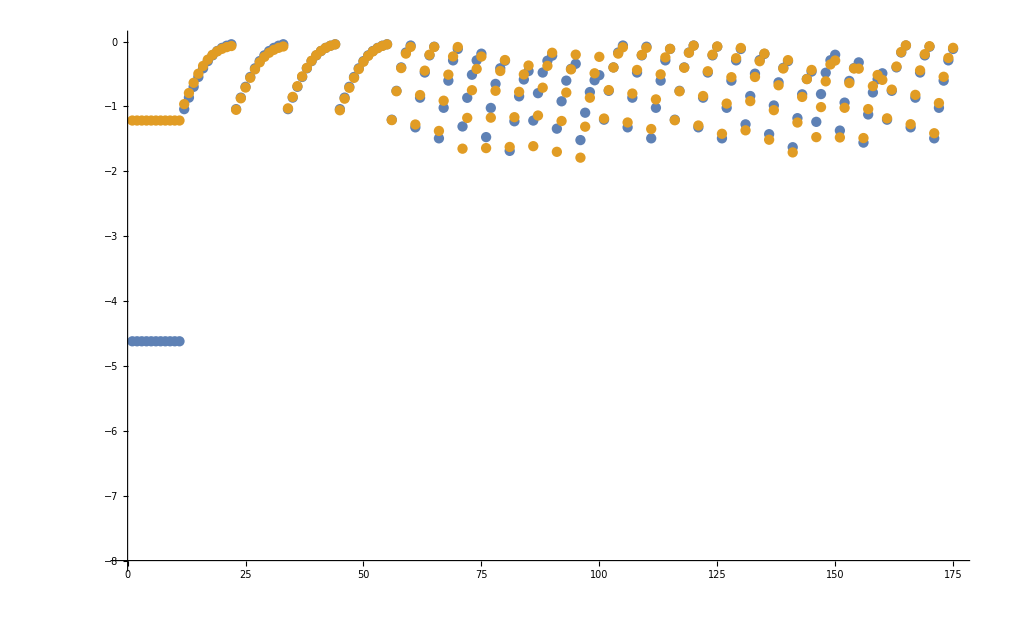

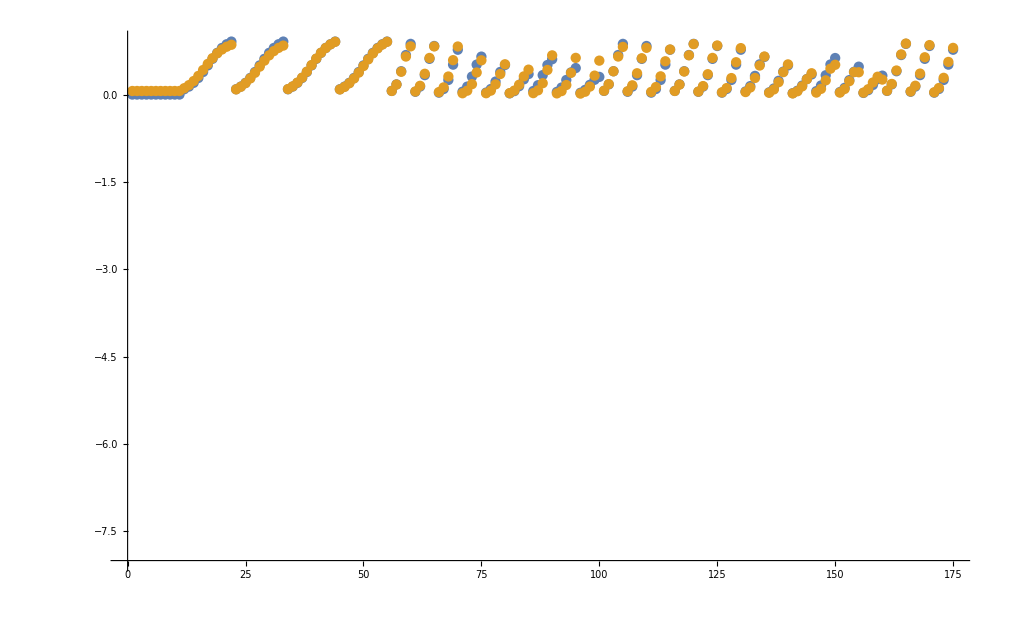

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.0000451708 | 0.37958
0.00089 | 0.000891344 | 0.150985
0.00053 | 0.000530978 | 0.184466

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 1.20456×10^-6

```mathematica
backCalculateRatios[customRatiosList[[1]][[1]], customRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 0.0000934857

```mathematica
backCalculateRatios[haldaneRatiosList[[1]][[1]], haldaneRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.40816 | 0.0391769